```mathematica
SetDirectory[NotebookDirectory[]<>"Simulation/Simulation/bin/Release"];
```

```mathematica
Set[#,"--"<>ToString@#]&/@{
NodeCount,
CouplingRadius,
CouplingStrength,
TimeScale,
DiffusionConstant,
DeltaTime,
WarmupTime,
MeasurementInterval,
MaximumTime,
DelayTime,
Seed,
BifurcationParameterMean,
BifurcationParameterVariance,
SpikeActivationThreshold,
SpikePeakThreshold
};
Set[#,ToString@#]&/@{
Config,
Trajectory,
InterspikeInterval
};
```

```mathematica
Read2DData[file_,type_]:=With[{n=BinaryRead[file,"Integer32"]},
Table[With[{m=BinaryRead[file,"Integer32"]},
Table[BinaryRead[file,type],{j,m}]
],{i,n}]
];
```

```mathematica
RunCommand[args__]:=RunProcess[{"Simulation.exe",args},"StandardOutput"];
GetConfig[guid_]:=Association@@(#[[1]]->ToExpression[#[[3,1]]]&/@Import["./Data/"<>guid<>"/Config.xml"][[2,3]])
GetTrajectory[guid_]:=Transpose@Read2DData["./Data/"<>guid<>"/Trajectory.bin","Real64"];
GetInterspikeInterval[guid_]:=Read2DData["./Data/"<>guid<>"/ISI.bin","Real64"];
ClearData[guid_]:=DeleteDirectory["./Data/"<>guid,DeleteContents->True];
RunSeries[variable_,values_,fixedArgs__]:=RunCommand[variable,#,fixedArgs]&/@values;
```

```mathematica
PlotTrajectory[guid_]:=With[{traj=GetTrajectory@guid},
ArrayPlot@traj];
PlotInterspikeIntervalPDF[guid_]:=With[{isi=GetInterspikeInterval@guid},
Histogram@Flatten@isi];
```

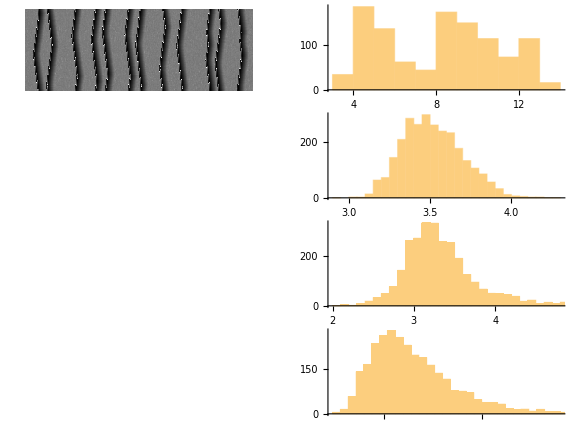

```mathematica
With[{guids=RunSeries[DiffusionConstant,{0.00012,0.001,0.005,0.05},
Config,
Trajectory,
InterspikeInterval]},
With[{result=GraphicsGrid[Transpose@{
PlotTrajectory/@guids,
PlotInterspikeIntervalPDF/@guids},
ImageSize->Large]},
ClearData/@guids;
result]]
```